## Setup

### PDE solver

```mathematica
ClearAll@runTwoComponentSim;
Options[runTwoComponentSim]=Join[Options[NDSolve],{"GridPoints"->100,"BC"->"Reflective"}];
runTwoComponentSim[{fhat_,uSource_,vSource_},params_,{nInit_,etaInit_},tMax_,opts:OptionsPattern[]]:=First@NDSolve[{
D[n[x,t],t]==Dv D[eta[x,t],{x,2}]
+(eps (uSource+vSource)/.{n->n[x,t],η->eta[x,t]}),D[eta[x,t],t]==Dv (1+Du/Dv) D[eta[x,t],{x,2}]-Du D[n[x,t],{x,2}]
+(-fhat+eps(Du/Dv uSource+vSource)/.{n->n[x,t],η->eta[x,t]}),
If[OptionValue["BC"]==="Periodic",
{(* periodic BCs *)
n[0,t]==n[L,t],eta[0,t]==eta[L,t],(D[n[x,t],x]/.x->0)==(D[n[x,t],x]/.x->L),(D[eta[x,t],x]/.x->0)==(D[eta[x,t],x]/.x->L)
},
{(* no-flux BCs *)
(D[n[x,t],x]/.x->0)==0,(D[eta[x,t],x]/.x->0)==0,(D[n[x,t],x]/.x->L)==0,(D[eta[x,t],x]/.x->L)==0
}
],
(* initial condition *)
n[x,0]==nInit[x],
eta[x,0]==etaInit[x]
}/.params,
{n,eta},
{x,0,L/.params},
{t,0,tMax},
Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->1},"Method"->{"IDA","ImplicitSolver"->"Newton"}}
];
```

### Finite difference equations for stationary state

```mathematica
discreteLaplace[data_,dx_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,2]/dx^2
]
```

```mathematica
ClearAll@setupFiniteDifferenceEqs;
setupFiniteDifferenceEqs[{fhat_,uSource_,vSource_},gridRes_]:=With[{
nVec=Thread[n@Range[gridRes]],
etaVec=Thread[eta@Range[gridRes]]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"nVec"->nVec,
"etaVec"->etaVec,
"Vars"->Join[nVec,etaVec],
"Eqs"->{
Dv discreteLaplace[etaVec,L/gridRes]
+(eps(uSource+vSource)/.{n->nVec,η->etaVec}),
Dv (1+Du/Dv) discreteLaplace[etaVec,L/gridRes]
-Du discreteLaplace[nVec,L/gridRes]
+(-fhat+eps(Du/Dv uSource+vSource)/.{n->nVec,η->etaVec})
}
|>
]
```

```mathematica
getInitGuess[fdSetup_,params_,initSol_]:=Join[
Transpose[{
fdSetup["nVec"],
n[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
Transpose[{
fdSetup["etaVec"],
eta[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}]
]
```

### Jacobian

```mathematica
laplaceMatrixAS[n_]:=SparseArray[{
{1,1}->-1,{-1,-1}->-3,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]
```

```mathematica
laplaceMatrixS[n_]:=SparseArray[{
{1,1}->-1,{-1,-1}->-1,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]
```

```mathematica
Options@constructGluedJacobianAS={"Reverse"->False};
constructGluedJacobianAS[fdSetup_,params_,statSol_,dfdu_,OptionsPattern[]]:=
With[{
solVec=If[OptionValue["Reverse"]===True,Reverse@#,#]&@Transpose[{
fdSetup["nVec"]/.statSol,
fdSetup["etaVec"]/.statSol
}],
dfduP=dfdu/.params,
gridRes=Length@statSol/2
},
KroneckerProduct[laplaceMatrixAS[gridRes],{{0,Dv},{-Du,Dv(1+Du/Dv)}}/(L/gridRes)^2/.params]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{n,η}->solVec[[i]]]),
{i,gridRes}
]
]
]
```

```mathematica
constructGluedJacobianS[fdSetup_,params_,statSol_,dfdu_]:=
With[{
solVec=Transpose[{
fdSetup["nVec"]/.statSol,
fdSetup["etaVec"]/.statSol
}],
dfduP=dfdu/.params,
gridRes=Length@statSol/2
},
KroneckerProduct[laplaceMatrixS[gridRes],{{0,Dv},{-Du,Dv(1+Du/Dv)}}/(L/gridRes)^2/.params]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{n,η}->solVec[[i]]]),
{i,gridRes}
]
]
]
```

### Finite-differences setup for the mass-conserving system

```mathematica
ClearAll@setupFiniteDifferenceEqsMC;
setupFiniteDifferenceEqsMC[f_,gridRes_]:=With[{
nVec=Thread[n@Range[gridRes]],
etaVec=Thread[eta@Range[gridRes]]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"nVec"->nVec,
"Vars"->Join[nVec,{eta}],
"Eqs"->{
Du discreteLaplace[nVec,L/gridRes]+(f/.{n->nVec,η->eta}),
Total@nVec-gridRes p
}
|>
]
```

```mathematica
getInitGuessMC[fdSetup_,params_,initSol_,Teval_]:=Join[
Transpose[{
fdSetup["nVec"],
n[x,Teval]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
{{eta,eta[0,Teval]/.params/.initSol}}
]
```

## Constant reaction-rate peak-forming model

### Model setup const. reac. rate model

Const-reaction-rate reaction kinetics in (n,η) variables

```mathematica
f=(η-10n/(1+n^2));
source=(p-n);
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[{f,source,0},400];
fdSetupMC=setupFiniteDifferenceEqsMC[f,400];
```

```mathematica
fixedParams={p->4,Du->1,L->200/2,T->1000};
params=Join[{eps->10^(-3),Dv->1000},fixedParams];
```

```mathematica
rhobar=4;
```

```mathematica
dx[fdSetup_]:=L*(fdSetup["UnitGrid"][[2]]-fdSetup["UnitGrid"][[1]]);
```

### Mass-conserving stationary state

```mathematica
initRunMC=runTwoComponentSim[
{f,0,0},
params,
{
rhobar*L/10*Sech[#/10]^2&,
0&
},
T/.fixedParams
];
```

```mathematica
statSolMC=Block[{n,eta},FindRoot[
fdSetupMC["Eqs"]/.p->rhobar/.params,
getInitGuessMC[fdSetupMC,params,initRunMC,T/.params],
AccuracyGoal->10,
PrecisionGoal->10,
WorkingPrecision->100,
MaxIterations->100
]
];
```

InterpolatingFunction::dmval: Input value {0.00204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

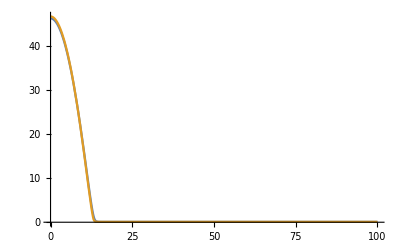

```mathematica
Plot[{Interpolation[Transpose@{fdSetupMC["UnitGrid"]*L/.params,fdSetupMC["nVec"]/.statSolMC}][x],n[x,T]/.params/.initRunMC},{x,0,L/.params},
PlotRange->All]
```

Calculate the distribution of mass uptake, i.e., the mass mode:

```mathematica
{evalsMCS,evecsMCS}=Last@SortBy[Transpose@Eigensystem[Normal@constructGluedJacobianS[
fdSetup,
params,
Join[Thread[fdSetup["etaVec"]->(eta/.statSolMC)],DeleteCases[statSolMC,eta->_]],
D[{0,-f},{{n,η}}]
],-5,Method->{"Arnoldi",Tolerance->10^-10}],#[[1]]&];
```

zero mode

```mathematica
evalsMCS
```

-1.947812006054397485450309034531722190353762984645318164487653977482193436581589516635864892209662328×10^-111

```mathematica
massDModeNorm=evecsMCS[[;;;;2]]/(dx[fdSetupMC]*Total[evecsMCS[[;;;;2]]])/.params;
dEtadM=Mean[evecsMCS[[2;;;;2]]/(2*dx[fdSetupMC]*Total[evecsMCS[[;;;;2]]])/.params];
```

```mathematica
lInt=1/(massDModeNorm.massDModeNorm* dx[fdSetupMC])/.params
```

13.2477

#### Non mass-conserving stat. state

```mathematica
initRunLS=runTwoComponentSim[
{f,source,0},
params,
{
rhobar*L/4Sech[#/4]^2&,
0&
},
T/.fixedParams
];
```

```mathematica
statSolLS=Block[{n,eta},FindRoot[
fdSetup["Eqs"]/.params,
getInitGuess[fdSetup,params,initRunLS],
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->100,
MaxIterations->100
]
];
```

#### Approximations

We neglect ρ_- relative to p

```mathematica
etaOffset=-eps*Total[massDModeNorm*(source/.n->fdSetupMC["nVec"]/.statSolMC)]*dx[fdSetupMC]/.params;
```

```mathematica
rhoOffset=etaOffset/10+eps*p(1+Du/Dv*1/10)/10/.params;
```

```mathematica
plateauEtaProfile=(eta/.statSolMC)+(eps*p/(2*Dv)(L^2-y^2)/.y->(-L+fdSetupMC["UnitGrid"]*L))+etaOffset/.params;
```

```mathematica
plateauRhoProfile=(fdSetupMC["nVec"][[-1]]/.statSolMC)+(eps*p/(2*Dv)(L^2-y^2)/.y->(-L+fdSetupMC["UnitGrid"]*L))/10+rhoOffset/.params;
```

#### Plots

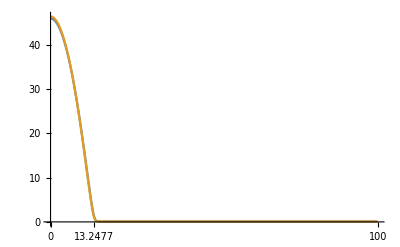

```mathematica
ListLinePlot[Transpose/@{{L*fdSetupMC["UnitGrid"]/.params,fdSetupMC["nVec"]/.statSolLS},{L*fdSetupMC["UnitGrid"]/.params,fdSetupMC["nVec"]/.statSolMC}},
PlotRange->All,
Ticks->{{0,lInt,L}/.params,None}]
```

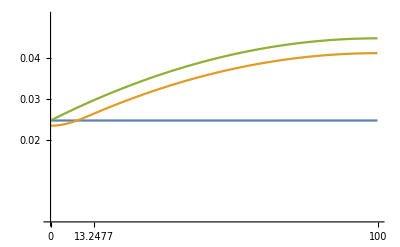

```mathematica
ListLinePlot[Transpose/@{
{L*fdSetupMC["UnitGrid"]/.params,Array[1&,Length@fdSetupMC["nVec"]]*(etaOffset)},{L*fdSetup["UnitGrid"]/.params,((fdSetup["etaVec"]/.statSolLS)-(eta/.statSolMC))},{L*fdSetup["UnitGrid"]/.params,(plateauEtaProfile-(eta/.statSolMC))}},
PlotRange->{All,{0,0.05}},
Ticks->{{0,lInt,L}/.params,{0.02,0.03,0.04,0.06,0.4}}]
```

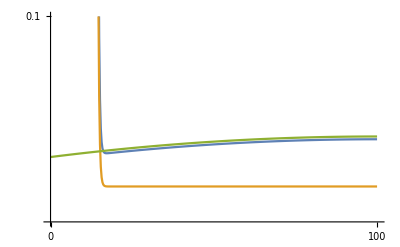

```mathematica
ListLinePlot[Transpose/@{{L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.statSolLS},{L*fdSetupMC["UnitGrid"]/.params,fdSetupMC["nVec"]/.statSolMC},{L*fdSetupMC["UnitGrid"]/.params,plateauRhoProfile}},
PlotRange->{{0,L}/.params,{0.08,0.1}},
Ticks->{{0,L}/.params,{0.1,0.2}}]
```

## Cubic Model

### Model setup cubic model

Const-reaction-rate reaction kinetics in (n,η) variables

```mathematica
f=(η-n^3+n);
source=(p-n);
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[{f,source,0},200];
fdSetupMC=setupFiniteDifferenceEqsMC[f,200];
```

```mathematica
fixedParams={p->-2/10,Du->1,L->40/2,T->1000};
params=Join[{eps->10^(-2),Dv->10},fixedParams];
```

```mathematica
rhobar=-2/10;
```

```mathematica
dx[fdSetup_]:=L*(fdSetup["UnitGrid"][[2]]-fdSetup["UnitGrid"][[1]]);
```

#### Mass-conserving Stat. state

```mathematica
initRunMC=runTwoComponentSim[
{f,0,0},
params,
{
rhobar+0.3Cos[Pi*#/L]&,
0&
},
T/.fixedParams
];
```

```mathematica
statSolMC=Block[{n,eta},FindRoot[
fdSetupMC["Eqs"]/.p->rhobar/.params,
getInitGuessMC[fdSetupMC,params,initRunMC,T/.params],
AccuracyGoal->10,
PrecisionGoal->10,
WorkingPrecision->100,
MaxIterations->100
]
];
```

Calculate the distribution of mass uptake, i.e., mass mode:

```mathematica
{evalsMCS,evecsMCS}=Last@SortBy[Transpose@Eigensystem[Normal@constructGluedJacobianS[
fdSetup,
params,
Join[Thread[fdSetup["etaVec"]->(eta/.statSolMC)],DeleteCases[statSolMC,eta->_]],
D[{0,-f},{{n,η}}]
],-5,Method->{"Arnoldi",Tolerance->10^-10}],#[[1]]&];
```

zero mode

```mathematica
evalsMCS
```

1.6353974164888470915554568044710560703145551609367679051146361062533408919544971228528958412697671819×10^-119

```mathematica
massDModeNorm=evecsMCS[[;;;;2]]/(dx[fdSetupMC]*Total[evecsMCS[[;;;;2]]])/.params;
dEtadM=Mean[evecsMCS[[2;;;;2]]/(2*dx[fdSetupMC]*Total[evecsMCS[[;;;;2]]])/.params];
```

```mathematica
lInt=1/(massDModeNorm.massDModeNorm*dx[fdSetupMC])/.params
```

4.24052

#### Non mass-conserving stat. state

```mathematica
initRunLS=runTwoComponentSim[
{f,source,0},
params,
{
rhobar+Cos[Pi*#/L]&,
0&
},
T/.fixedParams
];
```

```mathematica
statSolLS=Block[{n,eta},FindRoot[
fdSetup["Eqs"]/.params,
getInitGuess[fdSetup,params,initRunLS],
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->100,
MaxIterations->100
]
];
```

#### Approximations

```mathematica
xiP=(rhobar+1)/2
```

2/5

```mathematica
xiM=1-xiP
```

3/5

```mathematica
etaOffset=-eps*Total[massDModeNorm*(source/.n->fdSetupMC["nVec"]/.statSolMC)]*dx[fdSetupMC]/.params;
```

```mathematica
rhoOffsetL=etaOffset/2+eps*(p+1)(1+Du/Dv*1/2)/2/.params;
rhoOffsetU=etaOffset/2+eps*(p-1)(1+Du/Dv*1/2)/2/.params;
```

```mathematica
plateauEtaProfileL=(eta/.statSolMC)+(eps*(p+1)/(2*Dv)((xiM L)^2-x^2)/.x->(fdSetupMC["UnitGrid"]*L))+etaOffset/.params;
plateauEtaProfileU=(eta/.statSolMC)+(eps*Abs[p-1]/(2*Dv)(-(xiP L)^2+x^2)/.x->(fdSetupMC["UnitGrid"]*L))+etaOffset/.params;
```

```mathematica
plateauRhoProfileL=(fdSetupMC["nVec"][[-1]]/.statSolMC)+(eps*(p+1)/(2*Dv)((xiM L)^2-x^2)/.x->(fdSetupMC["UnitGrid"]*L))/2+rhoOffsetL/.params;
plateauRhoProfileU=(fdSetupMC["nVec"][[1]]/.statSolMC)+(eps*Abs[p-1]/(2*Dv)(-(xiP L)^2+x^2)/.x->(fdSetupMC["UnitGrid"]*L))/2+rhoOffsetU/.params;
```

#### Plots

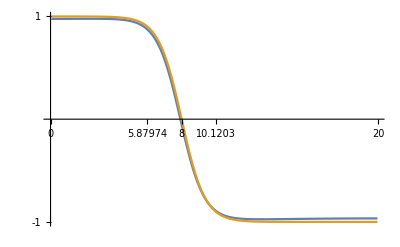

```mathematica
ListLinePlot[Transpose/@{{L*fdSetupMC["UnitGrid"]/.params,fdSetupMC["nVec"]/.statSolLS},{L*fdSetupMC["UnitGrid"]/.params,fdSetupMC["nVec"]/.statSolMC}},
PlotRange->All,
Ticks->{{0,xiP*L-lInt/2,xiP*L,xiP*L+lInt/2,L}/.params,{-1,1}}]
```

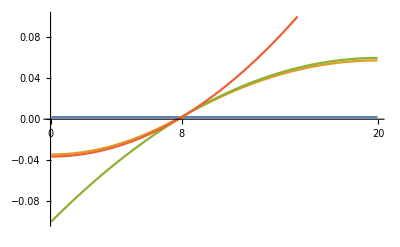

```mathematica
ListLinePlot[Transpose/@{
{L*fdSetupMC["UnitGrid"]/.params,Array[1&,Length@fdSetupMC["nVec"]]*(etaOffset)},{L*fdSetup["UnitGrid"]/.params,((fdSetup["etaVec"]/.statSolLS)-(eta/.statSolMC))},{L*Reverse@fdSetup["UnitGrid"]/.params,(plateauEtaProfileL-(eta/.statSolMC))},
{L*fdSetup["UnitGrid"]/.params,(plateauEtaProfileU-(eta/.statSolMC))}},
PlotRange->{All,{-0.1,0.1}},
Ticks->{{0,xiP*L,L}/.params,None}]
```

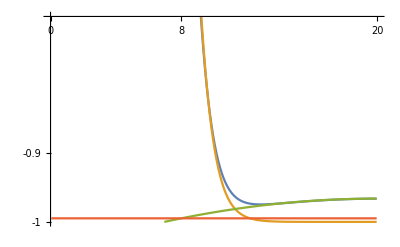

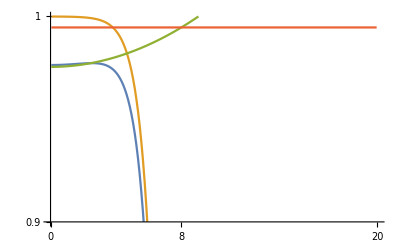

```mathematica
ListLinePlot[Transpose/@{{L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.statSolLS},{L*fdSetupMC["UnitGrid"]/.params,fdSetupMC["nVec"]/.statSolMC},{L*Reverse@fdSetupMC["UnitGrid"]/.params,plateauRhoProfileL},
{L*Reverse@fdSetupMC["UnitGrid"]/.params,Array[1&,Length@fdSetup["UnitGrid"]]*((fdSetupMC["nVec"][[-1]]/.statSolMC)+rhoOffsetL)}},
PlotRange->{{0,L}/.params,{-1,-0.7}},
Ticks->{{0,xiP*L,L}/.params,{-1,-0.9}}]
ListLinePlot[Transpose/@{{L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.statSolLS},{L*fdSetupMC["UnitGrid"]/.params,fdSetupMC["nVec"]/.statSolMC},{L*fdSetupMC["UnitGrid"]/.params,plateauRhoProfileU},
{L*Reverse@fdSetupMC["UnitGrid"]/.params,Array[1&,Length@fdSetup["UnitGrid"]]*((fdSetupMC["nVec"][[1]]/.statSolMC)+rhoOffsetU)}},
PlotRange->{(*{-0.4*2*L,0.4*2*L}*){0,L}/.params,{0.9,1}},
Ticks->{{0,xiP*L,L}/.params,{0.9,1}}]
```